# Delft’s Silicon device

reference: https://arxiv.org/abs/2202.09252
scientific contributors: Fernando, Simon

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Connectivity of this device

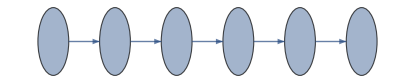

```mathematica
Graph[Range[0,5],Table[j->j+1,{j,0,4}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

Set the default configuration of the device

```mathematica
Options[SiliconDelft]={
qubitsNum->6,
(*average of T1*)
T1->100,
(* T2* *)
T2s-><|0->3,1-> 2.5,2-> 3.7,3-> 3.7,4-> 5.9,5-> 5.1|>,
(* T2 obtained by echo RX[π/2]-τ-RX[π]-τ-RX[π/2], where τ=1μs *)
T2-><|0->14,1-> 21.1,2-> 40.1,3-> 37.2,4-> 44.7,5-> 26.7|>,
(* If true, then the noise model uses T2s otherwise T2 *)
DDActive->True,
(* Rabi frequency of each qubit in MHz *)
RabiFreq-><|0->15.62*10^3,1-> 15.88*10^3,2-> 16.3*10^3,3-> 16.1*10^3,4-> 15.9*10^3,5-> 15.69*10^3|>,
(* The electromagnetic field in Tesla *)
BField->0.576,
(* Fidelities of X- and Y- rotations by random benchmarking *)
FidSingleXY-><|0->0.9977,1-> 0.9987,2-> 0.9996,3-> 0.9988,4-> 0.9991,5-> 0.9989|>,
FreqSingleXY->5,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingleXY->{0,1},
(*  The rabi Frequency (MHz) and fidelities of controlled-Z, C[Z], nearest-neighbors, where the control qubits are the lower one. Keys are the control qubits *)
FreqCZ-><|0->12.1,1-> 11.1,2-> 6.6,3-> 9.8,4-> 5.4|>,
FidCZ-><|0->0.8961173996 ,1->0.903347176,2-> 0.8837068241 ,3->0.9582985365,4-> 0.9426960894|>,
(* Error fraction/ratio {depolarising, dephasing} of controled-Rz rotation *)
EFCZ->{0.2,0.8},
(* Crosstalks error (C-Rz[ex])on the passive qubits when applying CZ gates;square matrix with dims nqubit-2*)
ExchangeRotOn->{{0,0.023, 0.018 ,0.03, 0.04},{0.05 ,0,0.03, 0.03, 0.04},{0.05, 0.03 ,0,0.07, 0.042},{0.038 ,0.03 ,0.031,0 ,0.25},{0.033, 0.03 ,0.02, 0.03,0}},
(* Crosstalks error (C-Rz[ex])on the passive qubits when no CZ gates applied *)
ExchangeRotOff-><|0->0.039,1-> 0.015 ,2->0.03 ,3->0.02,4-> 0.028|>,

(* Initialisation fidelity and duration*)
FidInit-><|"01"->0.9968,"012"->0.9934,"345"->0.9934,"45"->0.9968|>,
DurInit-><|"01"->20.2,"012"->30.6,"345"->30.6,"45"->20.2|>,
(* Readout fidelity and duration*)
FidMeas-><|"01"->0.9968,"012"->0.9946,"345"->0.9946,"45"->0.9968|>,
DurMeas-><|"01"->20.2,"012"->61,"345"->61,"45"->20.2|>,

(* error fraction of the 2-qubit error on QND readout qubit 01 and 45. Other errors are derived from the CRotX errors *)
EFRead->{0.4,0.6}
};
```

Native gates:
 Rx_j[θ],  Ry_j[θ],  Rz_j[θ],  C_i[Z_(i+1)], Wait_-1[Δt] 
 C_i[Rx_j[θ]] (for measurement only. (classical)conditional rotation.)

## Tests

```mathematica
ψ=CreateQureg[6];
ρ=CreateDensityQureg[6];
```

Remarks:
the time unit is μs

### Individual gate tests, complex passive noise

```mathematica
dev=SiliconDelft[];
```

Single qubit gates: x- and y- rotations have the same error and z-rotations are virtual, instaneous

{{0,{Rx_0[π/2],Depol_0[0],Deph_0[0.00345],U_1[{{-0.128249+0.0165056 ⅈ,0.-0.991605 ⅈ},{0.-0.991605 ⅈ,-0.128249-0.0165056 ⅈ}}],U_2[{{-0.584304+0.0352959 ⅈ,0.-0.810767 ⅈ},{0.-0.810767 ⅈ,-0.584304-0.0352959 ⅈ}}],U_3[{{-0.881336+0.0145127 ⅈ,0.-0.472268 ⅈ},{0.-0.472268 ⅈ,-0.881336-0.0145127 ⅈ}}],U_4[{{0.389495-0.0165075 ⅈ,0.+0.920881 ⅈ},{0.+0.920881 ⅈ,0.389495+0.0165075 ⅈ}}],U_5[{{0.000550664-0.992422 ⅈ,-0.122877},{-0.122877,-0.000550664-0.992422 ⅈ}}]},{C_0[Rz_1[0]],Deph_0[0],Depol_0[0],C_1[Rz_2[0.000238732]],Deph_1[0.00118343],Depol_1[0.000374906],C_2[Rz_3[0.000477465]],Deph_2[0.000623053],Depol_2[0.000374906],C_3[Rz_4[0.00031831]],Deph_3[0.000671592],Depol_3[0.000374906],C_4[Rz_5[0.000445634]],Deph_4[0.000558971],Depol_4[0.000374906],Deph_5[0.000935453],Depol_5[0.000374906]}},{1/20,{Rz_1[π]},{C_0[Rz_1[0]],Deph_0[0],Depol_0[0],C_1[Rz_2[0]],Deph_1[0],Depol_1[0],C_2[Rz_3[0]],Deph_2[0],Depol_2[0],C_3[Rz_4[0]],Deph_3[0],Depol_3[0],C_4[Rz_5[0]],Deph_4[0],Depol_4[0],Deph_5[0],Depol_5[0]}},{1/20,{C_0[Rz_1[0.0124141]],Deph_0[0.0344686],Depol_0[0.00746262]},{C_0[Rz_1[0]],Deph_0[0],Depol_0[0],C_1[Rz_2[0.00477465]],Deph_1[0.0231439],Depol_1[0.00746262],C_2[Rz_3[0.0095493]],Deph_2[0.0123146],Depol_2[0.00746262],C_3[Rz_4[0.0063662]],Deph_3[0.0132618],Depol_3[0.00746262],C_4[Rz_5[0.00891268]],Deph_4[0.0110615],Depol_4[0.00746262],Deph_5[0.0183802],Depol_5[0.00746262]}},{21/20,{Ry_3[2 π],Depol_3[0],Deph_3[0.0018],U_0[{{-0.885684+0.013836 ⅈ,0.+0.464083 ⅈ},{0.+0.464083 ⅈ,-0.885684-0.013836 ⅈ}}],U_1[{{0.00953594+0.0136627 ⅈ,0.+0.999861 ⅈ},{0.+0.999861 ⅈ,0.00953594-0.0136627 ⅈ}}],U_2[{{-0.724246-0.00856508 ⅈ,0.+0.689489 ⅈ},{0.+0.689489 ⅈ,-0.724246+0.00856508 ⅈ}}],U_4[{{-0.724246+0.00856508 ⅈ,0.+0.689489 ⅈ},{0.+0.689489 ⅈ,-0.724246-0.00856508 ⅈ}}],U_5[{{-0.771212+0.0162057 ⅈ,0.+0.636372 ⅈ},{0.+0.636372 ⅈ,-0.771212-0.0162057 ⅈ}}]},{C_0[Rz_1[0.00248282]],Deph_0[0.00709208],Depol_0[0.0014985],C_1[Rz_2[0.00095493]],Deph_1[0.00471695],Depol_1[0.0014985],C_2[Rz_3[0.00190986]],Deph_2[0.00248756],Depol_2[0.0014985],C_3[Rz_4[0]],Deph_3[0],Depol_3[0],C_4[Rz_5[0.00178254]],Deph_4[0.00223214],Depol_4[0.0014985],Deph_5[0.00373133],Depol_5[0.0014985]}},{5/4,{Rz_0[2 π]},{C_0[Rz_1[0]],Deph_0[0],Depol_0[0],C_1[Rz_2[0]],Deph_1[0],Depol_1[0],C_2[Rz_3[0]],Deph_2[0],Depol_2[0],C_3[Rz_4[0]],Deph_3[0],Depol_3[0],C_4[Rz_5[0]],Deph_4[0],Depol_4[0],Deph_5[0],Depol_5[0]}}}

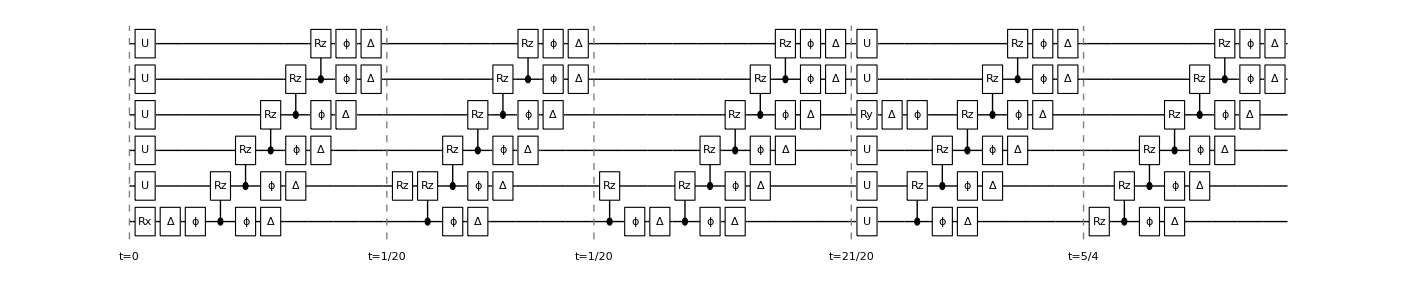

```mathematica
circ={Subscript[Rx, 0][π/2],Subscript[Rz, 1][π],Subscript[Wait, 0][1],Subscript[Ry, 3][2π],Subscript[Rz, 0][2π]};
InsertCircuitNoise[{#}&/@circ,dev,ReplaceAliases->False]//Chop
DrawCircuit[%]
```

Two qubit gates: CZ is obtained by π Z-rotation. CZ gates comes with dephasing, depolarising, and crosstalk.
The crosstalk when applying CZ is detemined. Thus, canceling out the crosstalk from passive noise.

{{0,{C_0[Z_1],Depol_(0,1)[0.0265732],Deph_(0,1)[0.106293],C_1[Rz_2[0.023]],C_2[Rz_3[0.018]],C_3[Rz_4[0.03]],C_4[Rz_5[0.04]],C_2[Rz_3[-0.000394599]],C_3[Rz_4[-0.000263066]],C_4[Rz_5[-0.000368292]]},{C_0[Rz_1[0.]],Deph_0[0.],Depol_0[0.],C_1[Rz_2[0.]],Deph_1[0.],Depol_1[0.],C_2[Rz_3[0.000394599]],Deph_2[0.000514975],Depol_2[0.000309853],C_3[Rz_4[0.000263066]],Deph_3[0.000555099],Depol_3[0.000309853],C_4[Rz_5[0.000368292]],Deph_4[0.000462005],Depol_4[0.000309853],Deph_5[0.000773228],Depol_5[0.000309853]}},{0.0413223,{C_4[Z_5],Depol_(4,5)[0.0145055],Deph_(4,5)[0.0580221],C_0[Rz_1[0.033]],C_1[Rz_2[0.03]],C_2[Rz_3[0.02]],C_3[Rz_4[0.03]],C_0[Rz_1[-0.00114945]],C_1[Rz_2[-0.000442097]],C_2[Rz_3[-0.000884194]],C_3[Rz_4[-0.000589463]]},{C_0[Rz_1[0.00114945]],Deph_0[0.00329597],Depol_0[0.000694123],C_1[Rz_2[0.000442097]],Deph_1[0.00218933],Depol_1[0.000694123],C_2[Rz_3[0.000884194]],Deph_2[0.00115319],Depol_2[0.000694123],C_3[Rz_4[0.000589463]],Deph_3[0.00124298],Depol_3[0.000694123],C_4[Rz_5[0.]],Deph_4[0.],Depol_4[0.],Deph_5[0.],Depol_5[0.]}}}

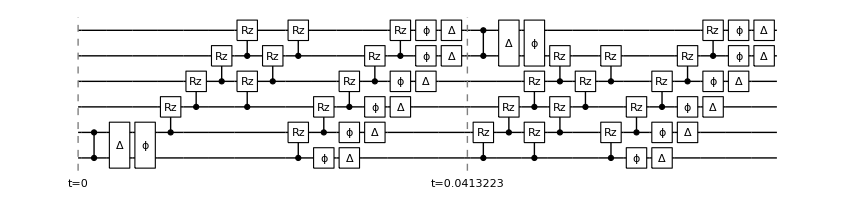

```mathematica
dev=SiliconDelft[];
InsertCircuitNoise[{{Subscript[C, 0][Subscript[Z, 1]]},{Subscript[C, 4][Subscript[Z, 5]]}},dev]
DrawCircuit[%]
```

## Reproducing results from the paper

### Initialisation fidelity goal: 0.95?

```mathematica
ApplyCircuit[InitZeroState@ψ,{Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]}];
```

```mathematica
(* initialise the qubits to mixed state *)
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[Init, 0,1,2],Subscript[Init, 3,4,5]},SiliconDelft[DDActive->False,EFSingleXY->{1,0},EFRead->{.5,.5}]]];
CalcFidelity[ρ,ψ]
```

0.993812

```mathematica
initfid[depolxy_?NumericQ,depolread_?NumericQ]:=Module[{},
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[Init, 0,1,2],Subscript[Init, 3,4,5],Subscript[M, 0,1,2],Subscript[M, 3,4,5]},SiliconDelft[DDActive->False,EFSingleXY->{depolxy,1.-depolxy},EFRead->{depolread,1.-depolread}]]];
Abs[0.995-CalcFidelity[ρ,ψ]]
]
```

NMinimize[{initfid[x, y], 0. <= x <= 1., 0. <= y <= 1.}, {x, y}, PrecisionGoal -> 2, MaxIterations -> 50]

$Aborted

### T_1 average with perfect measurement

```mathematica
ApplyCircuit[InitZeroState@ψ,{Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]}];
```

```mathematica
res1=Table[
(* initialise the qubits to mixed state *)
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@{Subscript[Init, 0,1,2],Subscript[Init, 3,4,5],Subscript[Wait, 0][t]},SiliconDelft[EFRead->{1,0}]]];
{t, CalcFidelity[ρ,ψ]^2}
,{t,Range[0,150,2]}];
```

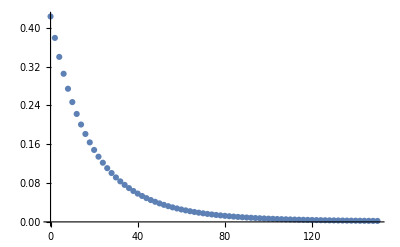

```mathematica
ListPlot[res1,PlotRange->All]
```

### Obtaining T_2 from T_2^* X90 - tau - X180 - tau - X90, tau = 1 us

```mathematica
Options[SiliconDelft,T2]
Options[SiliconDelft,T2s]
```

{T2→<|0→14,1→21.1,2→40.1,3→37.2,4→44.7,5→26.7|>}

{T2s→<|0→3,1→2.5,2→3.7,3→3.7,4→5.9,5→5.1|>}

Calculate the T2 of qubit 1

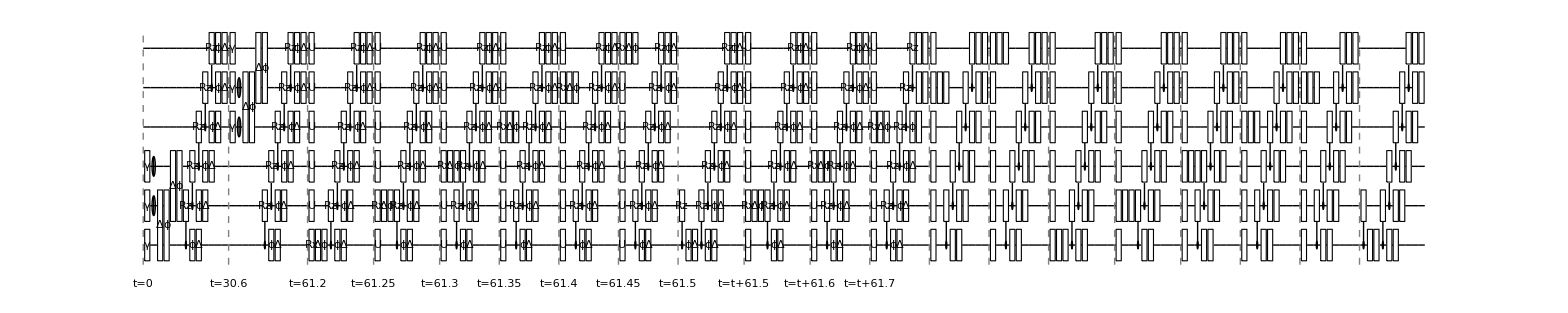

```mathematica
InsertCircuitNoise[SerializeCircuit@{Subscript[Init, 0,1,2],Subscript[Init, 3,4,5],Sequence@@(Subscript[Rx, #][π/2]&/@Range[0,5]),Subscript[Wait, 0][t],Sequence@@(Subscript[Rx, #][π]&/@Range[0,5]),Subscript[Wait, 0][t],Sequence@@(Subscript[Rx, #][π/2]&/@Range[4])},SiliconDelft[DDActive->False,T1->10]];
DrawCircuit@%
```

```mathematica
ApplyCircuit[InitZeroState@ψ,{Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]}];
res2=Table[
(* initialise the qubits to mixed state *)
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@{Subscript[Init, 0,1,2],Subscript[Init, 3,4,5],Sequence@@Table[If[(q===0)||(q===5),Subscript[Rx, q][π/2],Subscript[Rx, q][-π/2]],{q,Range[0,5]}],Subscript[Wait, 0][t],Sequence@@(Subscript[Rx, #][π]&/@Range[0,5]),Subscript[Wait, 0][t],Sequence@@(Subscript[Rx, #][π/2]&/@Range[0,5])},SiliconDelft[DDActive->False]]];
Table[{t,CalcProbOfOutcome[ρ,q,0]},{q,Range[0,5]}]
,{t,Range[0,40,2]}];
```

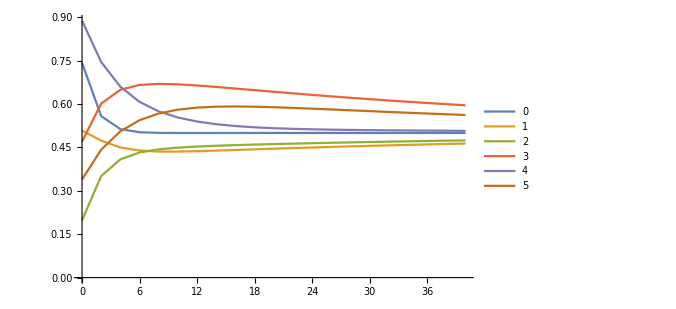

```mathematica
ListPlot[res2[[All,#]]&/@Range[6],PlotLegends->Range[0,5],Joined->True,PlotRange->All,ImageSize->500]
```

### Bell states (super bad because of off-resonant rabi osc)

-Graphics-

```mathematica
(*Return non-zero elements only *)
nonzero[list_]:=Select[Table[If[list[[i]]!=0,{i-1,list[[i]]}],{i,Length@list}],ListQ]
```

```mathematica
ψ2=CreateQureg[2];
ρ2=CreateDensityQureg[2];
```

Bell 01

```mathematica
circ={Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]};
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@{Subscript[Init, 0,1,2],Sequence@@circ},SiliconDelft[EFCZ->{1,0},EFSingleXY->{0,1}]]];
SetQuregMatrix[ρ2,PartialTrace[ρ,2,3,4,5]];
PlotDensityMatrix@ρ2
ApplyCircuit[InitZeroState@ψ2,{Subscript[X, 1],Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]}];
CalcFidelity[ρ2,ψ2]
```

-Graphics3D-

0.855222

Bell 12

```mathematica
circ={Subscript[Rx, 1][-π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][-π/2]};
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@{Subscript[Init, 0,1,2],Sequence@@circ},SiliconDelft[]]];
SetQuregMatrix[ρ2,PartialTrace[ρ,0,3,4,5]];
PlotDensityMatrix@ρ2

ApplyCircuit[InitZeroState@ψ2,{Subscript[X, 0],Subscript[X, 1],Subscript[Rx, 0][-π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2]}];
CalcFidelity[ρ2,ψ2]
```

-Graphics3D-

0.417313

Bell 23

```mathematica
circ={Subscript[Rx, 2][-π/2],Subscript[Rx, 3][π/2],Subscript[C, 2][Subscript[Z, 3]],Subscript[Rx, 3][-π/2]};
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@{Subscript[Init, 0,1,2],Subscript[Init, 3,4,5],Sequence@@circ},SiliconDelft[]]];
SetQuregMatrix[ρ2,PartialTrace[ρ,0,1,4,5]];
PlotDensityMatrix@ρ2

ApplyCircuit[InitZeroState@ψ2,{Subscript[X, 0],Subscript[X, 1],Subscript[Rx, 0][-π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2]}];
CalcFidelity[ρ2,ψ2]
```

-Graphics3D-

0.172989

Bell 34

```mathematica
circ={Subscript[Rx, 3][-π/2],Subscript[Rx, 4][π/2],Subscript[C, 3][Subscript[Z, 4]],Subscript[Rx, 4][-π/2]};
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@{Subscript[Init, 3,4,5],Sequence@@circ},SiliconDelft[]]];
SetQuregMatrix[ρ2,PartialTrace[ρ,0,1,2,5]];
PlotDensityMatrix@ρ2

ApplyCircuit[InitZeroState@ψ2,{Subscript[X, 0],Subscript[X, 1],Subscript[Rx, 0][-π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2]}];
CalcFidelity[ρ2,ψ2]
```

-Graphics3D-

0.161468

Bell 45

```mathematica
circ={Subscript[Rx, 4][-π/2],Subscript[Rx, 5][π/2],Subscript[C, 4][Subscript[Z, 5]],Subscript[Rx, 5][-π/2]};
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@{Subscript[Init, 3,4,5],Sequence@@circ},SiliconDelft[]]];
SetQuregMatrix[ρ2,PartialTrace[ρ,0,1,2,3]];
PlotDensityMatrix@ρ2

ApplyCircuit[InitZeroState@ψ2,{Subscript[X, 0],Subscript[Rx, 0][-π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2]}];
CalcFidelity[ρ2,ψ2]
```

-Graphics3D-

0.306025

### 3 - qubits GHZ (super bad because of off-resonant rabi osc)

```mathematica
ψ3=CreateQureg[3];
ρ3=CreateDensityQureg[3];
```

-Graphics-

GHZ 012

```mathematica
circ={Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][π/2]};
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@{Subscript[Init, 0,1,2],Sequence@@circ},SiliconDelft[]]];
SetQuregMatrix[ρ3,PartialTrace[ρ,3,4,5]];
PlotDensityMatrix@ρ3

ApplyCircuit[InitZeroState@ψ3,{Subscript[X, 1],Subscript[X, 2],Sequence@@circ}];
CalcFidelity[ρ3,ψ3]
```

-Graphics3D-

0.0580749